# MATH299M/CMSC389W - Visualization through Mathematica Week 3: Plotting I: Plot, Options and Manipulate Controls

Plot and Plot Options

Plot is function that takes in two arguments, the first being a function in terms of a variable, the second being a specification of that range of that variable, then Options, which are specified by connecting the Option you want to set and the setting of it with an arrow (→). The function can of course use calls to other functions.

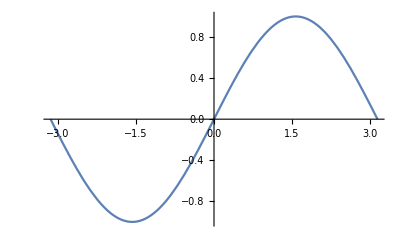

```mathematica
Plot[Sin[x],{x,-π,π}]
```

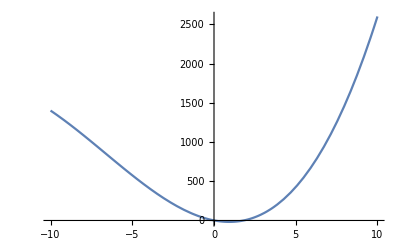

```mathematica
Plot[x^3+20 x^2-40x+1,{x,-10,10}]
```

You can plot multiple functions at the same time with Plot by feeding in a list of functions as the first argument, they are automatically assigned colors, which we’ll learn how to change.

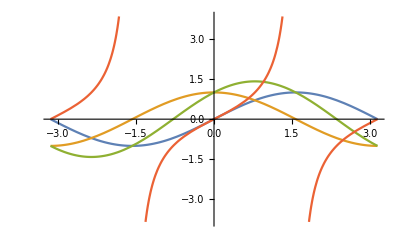

```mathematica
Plot[{Sin[x],Cos[x],Sin[x]+Cos[x],Tan[x]},{x,-π,π}]
```

### PlotRange

Now we introduce Options, which will make our Plots much nicer to look at. The first problem at hand is that the y-axis values hardly ever default to what we want. We can use PlotRange to specify the lower and upper bounds of the dependent axis with a 2-tuple; a single number n is shorthand for {-n,n}. First I show an example of how not setting the PlotRange is annoying because then when you want to compare graphs Mathematica scales the axis instead of the curve, but fixing the range handles that:

```mathematica
Manipulate[Plot[a*x^2,{x,-5,5}],{a,1,100}]
```

```mathematica
Manipulate[Plot[a*x^2,{x,-5,5},PlotRange->{-1,10}],{a,1,100}]
```

### AspectRatio

Personally I’m a big fan of fixing the aspect ratio of the box, I like it to be a square. This is particularly nice if your x range and y range are the same, because then the plot isn’t distorted. Use an arrow to connect AspectRatio to a number n to specify that you want the ratio of the dependent axis to the independent axis to be n. PlotRange always defaults to something that I think looks a little vertically squashed. Also square’s look nice inside of Manipulates.

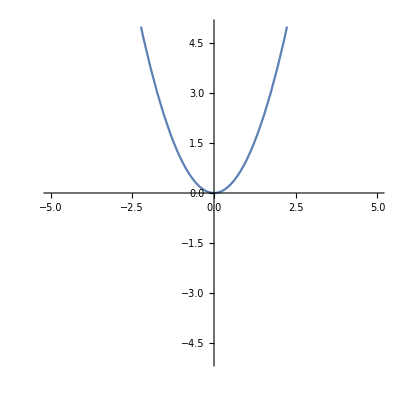

{,}

```mathematica
Plot[x^2,{x,-5,5},PlotRange->5,AspectRatio->1]
{Manipulate[Plot[a*x^2,{x,-5,5},PlotRange->5,AspectRatio->1],{a,-5,5}],Manipulate[Plot[a*x^2,{x,-5,5},PlotRange->5,AspectRatio->.25],{a,-5,5}]}
```

Isn’t that second one horrible? Ew. Squares are good.

### ImageSize

Like many Options, you’ll see later in the course that you can use the ImageSize Option on other kinds of model. There are 5 presets for ImageSize, Tiny, Small, Medium, Large and Full, or you can put in a number to specify exactly how large you want it. Full takes up the entire window, it’s very obnoxious, not recommended.

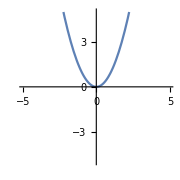
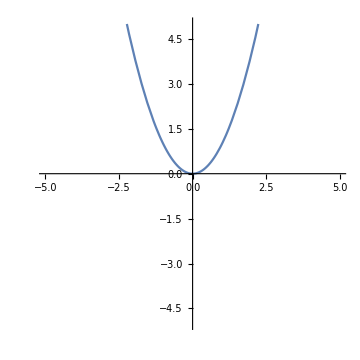
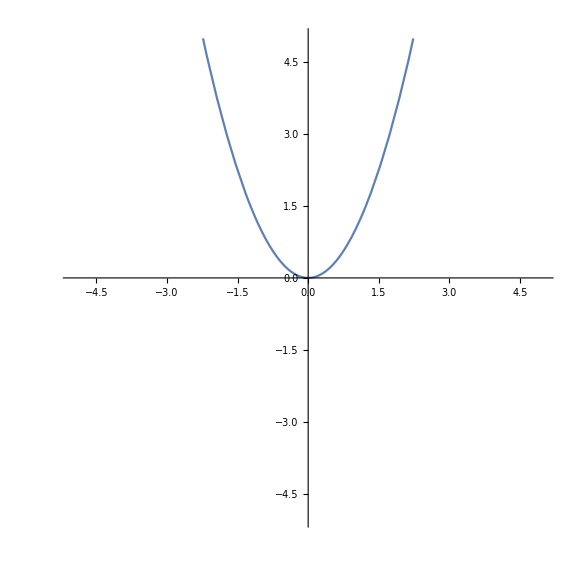
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Plot[x^2,{x,-5,5},PlotRange->5,AspectRatio->1,ImageSize->#]&,{Tiny,Small,Medium,Large}]
```

```mathematica
Plot[x^2,{x,-5,5},PlotRange->5,AspectRatio->1,ImageSize->Full]
```

-Graphics-

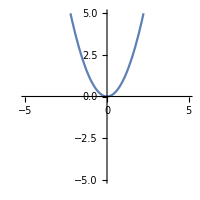
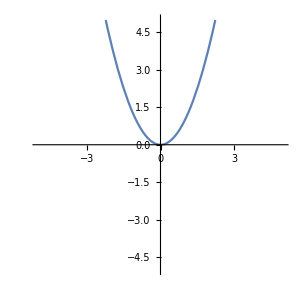
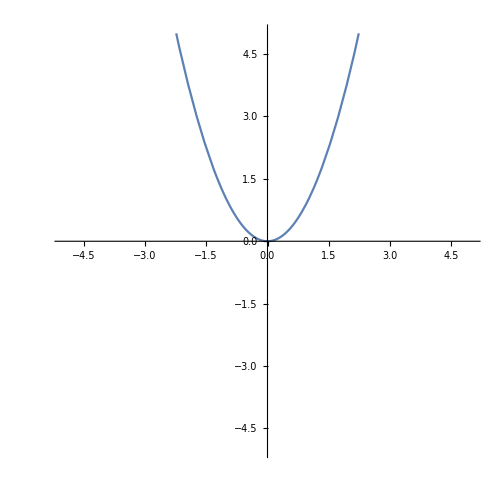
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Plot[x^2,{x,-5,5},PlotRange->5,AspectRatio->1,ImageSize->#]&,{100,200,300,500}] (* Approximate Absolute Sizes of Tiny, Small, Medium and Large *)
```

### PlotLabel

Simply puts a title at the top of the graph. You can use Style[] around the text you want there to make it look nicer; Style takes in a string and then

```mathematica
Manipulate[Plot[a*x^2,{x,-5,5},PlotLabel->"Quadratic"],{a,1,100}]
```

```mathematica
Manipulate[Plot[a*x^2,{x,-5,5},PlotLabel->Style["Quadratic",Red,Bold,15]],{a,1,100}]
```

You can also put the dependent variable in the PlotTitle, which is particularly nice for when you are Manipulating the Plot, so the user always knows what function they’re looking at.

```mathematica
Manipulate[Plot[a*x^2,{x,-5,5},PlotRange->5,AspectRatio->1,PlotLabel->a*x^2],{a,-5,5}]
```

Also a reminder that Mathematica lets you put whatever you want in as arguments to a lot of things:

```mathematica
Plot[x^2,{x,-5,5},PlotRange->5,AspectRatio->1,ImageSize->Large,PlotLabel->Manipulate[Plot[a*Sin[y],{y,-5,5},PlotLabel->"PRE-STYLED TITLE"],{a,-5,5}]]; (* Unsupress this output to use *)
```

I have the outputted suppressed because it keeps dynamically updating as you scroll down, taking up resources - remove the semicolon then run it to see.

### AxesLabel

AxesLabel gives names to the axes, Automatic will give the independent axis the name of the variable you used and no name to the dependent axis. Using a 2-tuple you can specify the labels on both axes.

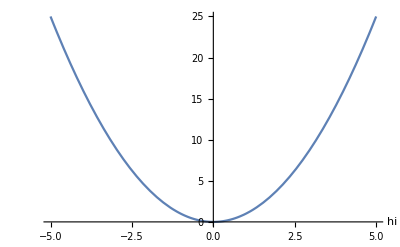

```mathematica
Plot[hi^2,{hi,-5,5},AxesLabel->Automatic]
```

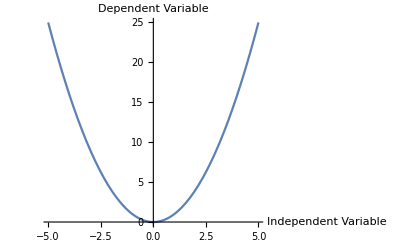

```mathematica
Plot[x^2,{x,-5,5},AxesLabel->{"Independent Variable","Dependent Variable"}]
```

### PlotLegend

PlotLegends gives you a key so that the user knows which curves are which when you plot multiple on the same Plot. Setting it to “Expressions” will give what the functions are in function notation, setting it to a tuple lets you explicitly name them.

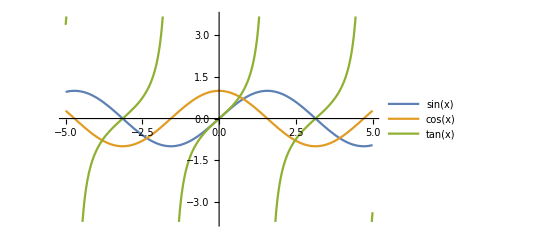

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-5,5},PlotLegends->"Expressions"]
```

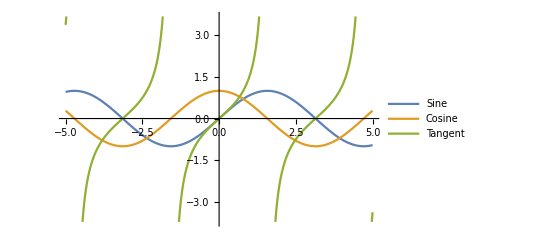

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-5,5},PlotLegends->{"Sine","Cosine","Tangent"}]
```

### PlotStyle

And finally the most fun Option, PlotStyle lets you pick the color of the curves, as well as some other things. As with all of these functions, the Wolfram documentation has all of the details.

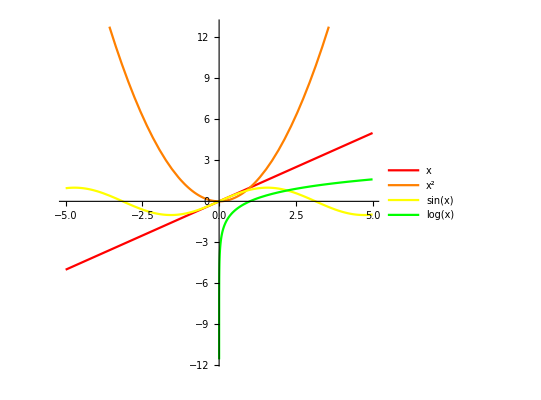

```mathematica
Plot[{x,x^2,Sin[x],Log[x]},{x,-5,5},AspectRatio->1,PlotLegends->"Expressions",PlotStyle->{Red,Orange,Yellow,Green}]
```

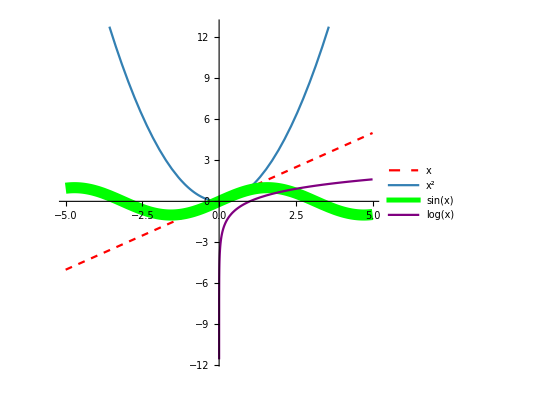

```mathematica
Plot[{x,x^2,Sin[x],Log[x]},{x,-5,5},AspectRatio->1,PlotLegends->"Expressions",PlotStyle->{{Red,Dashed},{RGBColor[.2,.5,.7],Thick},{Thickness[.02],Green},Purple}]
```

Manipulate Options

So far you’ve only used sliders to control things with Manipulate - here I’ll show you how to be fancier with sliders and how to use several other control types.

### Slider

What you’ve seen already is a Manipulate argument of the form {n,a,b} which gives you a slider for n from a to b. You can add a fourth element to this list to specify a step size, restricting the slider to move along intervals of that size. Furthermore, instead of just n, you can out a 2-tuple {n,c} where c is the initial value of the slider, or a 3-tuple where the third element is the name of the slider. So for sliders the full form goes: {{var,initialValue,name},lowerBound,upperBound,stepSize}.

```mathematica
Manipulate[Plot[a*x^2,{x,-5,5},AspectRatio->1,PlotRange->10],{{a,5,"Concavity"},-10,10,2}]
```

### Other Manipulate controls (a tad redundant, but the above model is a nice all-together example)

Slider

```mathematica
Manipulate[x,{x,-2,2}]
```

Slider step size

```mathematica
{Manipulate[x,{x,-5,5,1}],Manipulate[x,{x,-5,5,.5}],Manipulate[x,{x,-5,5,.5}]}
```

{,,}

Initial value

```mathematica
Manipulate[x,{{x,1.5},-2,2}]
```

Variable name

```mathematica
Manipulate[x,{{x,1.5,"X Value"},-2,2}]
```

Checkbox

```mathematica
Manipulate[x,{x,{True,False}}]
```

Option boxes

```mathematica
Manipulate[x,{x,{3,1,4,5,9}}]
```

Drop down box

```mathematica
Manipulate[x,{x,{3,1,4,5,9,6}}]
```

Option and drop down boxes with names

```mathematica
{Manipulate[x,{{x,3},{3->"Apple",1->"Orange",4,5->"Mango",9->"Lime"}}],Manipulate[x,{{x,1},{3->"Apple",1->"Pear",4,5->"Mango",9->"Dragon Fruit",6}}]}
```

{,}

Input Box

```mathematica
Manipulate[x,{{x,Null,"Input Here"}}]
```

Custom input function box

```mathematica
Manipulate[Plot[g/.(x->y),{y,-5,5},AspectRatio->1],{{g,x^2,"Custom"}},ControlPlacement->Left]
```

Manipulating multiple variables

```mathematica
Manipulate[{x,y},{{x,1},-5,5},{{y,0},-5,5}]
```

Control Placement

```mathematica
{Manipulate[x,{x,-2,2},ControlPlacement->Left],Manipulate[x,{x,-2,2},ControlPlacement->Top],Manipulate[x,{x,-2,2},ControlPlacement->Right],Manipulate[x,{x,-2,2},ControlPlacement->Bottom]}
```

{,,,}

Buttons

```mathematica
Manipulate[x,{{x,0},-5,5},Button["Reset to 0",{x=0}]]
```

Delimiters and text w/ Manipulate controls

```mathematica
Manipulate[x,"Slider Controls",{{x,0},-5,5},Delimiter,"Button Controls",Button["Reset to 0",{x=0;Print["Devan Stop"]}]]
```

Devan Stop

Devan Stop

Devan Stop

«7 more identical outputs»

Remove the Panel

```mathematica
Manipulate[x,{x,-5,5},Paneled->False]
```

Add a Frame

```mathematica
Framed[Manipulate[x,{x,-5,5},Paneled->False],FrameMargins->20,Background->Pink,BaseStyle->{FontColor->GrayLevel[.2]}]
```

### Just Because

Unfortunately the only way (for now) to have a slider etc. that has a Manipulate-able value in its definition is to nest Manipulates:

```mathematica
Manipulate[Manipulate[Plot[a*x^2,{x,-5,5},PlotRange->10,AspectRatio->1],{a,lowerBound,upperBound,stepSize}],{{lowerBound,-5},-100,100},{{upperBound,0},-100,100},{{stepSize,1},.01,10}]
```

But, please, don’t ever do this.

## Ajeet Gary - University of Maryland Experimental Geometry Lab MATH299M/CMSC389W Fall 2018 September 9th, 2018